```mathematica
Quit[]
```

```mathematica
AppendTo[$Path, NotebookDirectory[]];
```

```mathematica
Get["CubeAcquire.wl"]
Get["CubeVisualize.wl"]
Get["CubeCore.wl"]
```

```mathematica
cubeString = sampleStrings["solved"]
```

WWWWWWWWWOOOGGGRRRBBBOOOGGGRRRBBBOOOGGGRRRBBBYYYYYYYYY

## 2D Cube

```mathematica
cube2D = Generate2DCube[cubeString];
```

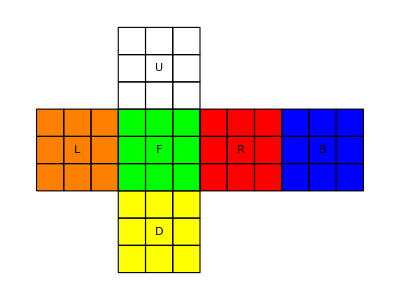

```mathematica
Visualize2DCube[cube2D];
```

## 3D Cube

```mathematica
cube3DPieces = GetPieces[cubeString];
```

```mathematica
cube3D = Dynamic[Generate3DCube[cube3DPieces]];
```

```mathematica
Visualize3DCube[cube3D];
```

-Graphics3D-